#### Hometask 1. Multi-criteria tasks

Compromise solution

```mathematica
f1[x1_,x2_]:=-x1+x2-6
f2[x1_,x2_]:=x1+x2+2
```

```mathematica
minf1=FindMinimum[{f1[x1,x2],13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{-10.,{x1→4.,x2→0.}}

```mathematica
maxf2=FindMaximum[{f2[x1,x2],13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{7.,{x1→4.,x2→1.}}

```mathematica
fGen[x1_,x2_,x3_]:=x3
```

```mathematica
FindMinimum[{fGen[x1,x2,x3],{x1,x2,x3}.{1,1,maxf2⟦1⟧}+2≥maxf2⟦1⟧&&{x1,x2,x3}.{-1,1,minf1⟦1⟧}-6≤minf1⟦1⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2&&x3≥0},{x1,x2,x3}]
```

{0.0588235,{x1→4.,x2→0.588235,x3→0.0588235}}

```mathematica
FindMaximum[{f2[x1,x2],(f1[x1,x2]≤ minf1⟦1⟧+0.1*minf1⟦1⟧)&&(13x1+26x2≤78)&&(0≤x1≤4)&&(0≤x2≤2)},{x1,x2}]
```

FindMaximum::nsol: There are no points that satisfy the constraints {-6-x1+x2≤-11.,13 x1+26 x2≤78,0≤x1≤4,0≤x2≤2}.

{-∞,{x1→Indeterminate,x2→Indeterminate}}

Two criteria

```mathematica
concs1={0.05,0.1,0.15}*minf1⟦1⟧;
concs2={0.1,0.15,0.2}*maxf2⟦1⟧;
```

```mathematica
FindMinimum[{f1[x1,x2],f2[x1,x2]≤maxf2⟦1⟧+concs2⟦1⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{-10.,{x1→4.,x2→0.}}

```mathematica
FindMinimum[{f1[x1,x2],f2[x1,x2]≤maxf2⟦1⟧+concs2⟦2⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{-10.,{x1→4.,x2→0.}}

```mathematica
FindMinimum[{f1[x1,x2],f2[x1,x2]≤maxf2⟦1⟧+concs2⟦3⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{-10.,{x1→4.,x2→0.}}

```mathematica
FindMaximum[{f2[x1,x2],f1[x1,x2]≥minf1⟦1⟧+concs1⟦1⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{7.,{x1→4.,x2→1.}}

```mathematica
FindMaximum[{f2[x1,x2],f1[x1,x2]≥minf1⟦1⟧+concs1⟦2⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{7.,{x1→4.,x2→1.}}

```mathematica
FindMaximum[{f2[x1,x2],f1[x1,x2]≥minf1⟦1⟧+concs1⟦3⟧&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

{7.,{x1→4.,x2→1.}}

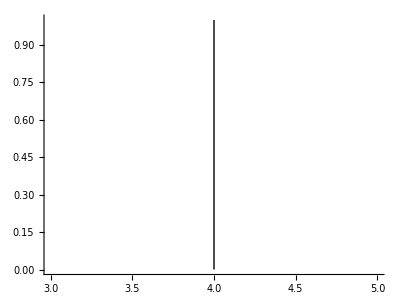

```mathematica
Graphics[{Line[{{4,0},{4,1}}]},Axes->True]
```

```mathematica
FindMaximum[{f2[x1,x2],f2[x1,x2]/maxf2⟦1⟧+f1[x1,x2]/minf1⟦1⟧==2&&13x1+26x2≤78&&0≤x1≤4&&0≤x2≤2},{x1,x2}]
```

FindMaximum::nsol: There are no points that satisfy the constraints {-0.1 (-6-x1+x2)+0.142857 (2+x1+x2)==2,13 x1+26 x2≤78,0≤x1≤4,0≤x2≤2}.

{-∞,{x1→Indeterminate,x2→Indeterminate}}